### Setup

```mathematica
(*Converts n to a binary string of length l*)
toBin[n_,l_]:= Join[ConstantArray[0,l-Length[IntegerDigits[n,2]]],IntegerDigits[n,2]]
(*The ordering of the game. The first entry has to be a total order*)
ordering = {t>r>s > p};

(*Normalize by setting the outside parameters to 1 and 0.*)
outside = {First[ordering[[1]]/.{Greater ->List}],Last[ordering[[1]]/.{Greater ->List}]};
values = {outside[[1]]==1,outside[[2]]==0};

inside = DeleteCases[ordering[[1]] /.{Greater->List},Alternatives @@ outside];
changes = values/.{Equal->Rule};
restrictions= ordering/.changes;


(*All restrictions*)
restrictions = Flatten[{ordering,values}];

(*All binary strategies*)
strats = Table[ Join[ConstantArray[0,4-Length[IntegerDigits[i,2]]],IntegerDigits[i,2]],{i,0,15}];
```

### Main Function for computing q-values

```mathematica
transitionEquation[q1_,q2_]:=q1*((1-epsilon/2)*Boole[q1>q2]+epsilon/2*Boole[q1<q2])+q2*((1-epsilon/2)*Boole[q1<q2]+epsilon/2*Boole[q1>q2]);

result[i_, strats_]:=
Module[{input = i, str = strats},
output = {};
transpoints = {};
(*States are 00, 01, 10, 11, given own action and response of opponent*)
(*1 is coop, 0 is defect*)
(*Reward function (when transitioning into that state): f(00) = p, f(01) = t, f(10) = s, f(11) = r *)
(*QXYYZ: X = Agent (1 or 2), YY = state, Z = response action*)
(*16 possible policies(2^4), so the loop is executed 16 times*)
(**)
Do[{
strat = str[[j]];
(*Get an ordering of the Q-values based on the strategy-pair*)
assumptions = Flatten[{
               If[strat[[1]]==0, Q1000>Q1001, Q1000<Q1001],
               If[strat[[2]]==0, Q1010>Q1011, Q1010<Q1011],
               If[strat[[3]]==0, Q1100>Q1101, Q1100<Q1101],
               If[strat[[4]]==0, Q1110>Q1111, Q1110<Q1111],
               If[input[[1]]==0, Q2000>Q2001, Q2000<Q2001],
               If[input[[2]]==0, Q2010>Q2011, Q2010<Q2011],
               If[input[[3]]==0, Q2100>Q2101, Q2100<Q2101],
               If[input[[4]]==0, Q2110>Q2111, Q2110<Q2111],
               ordering, 0 < epsilon < 1}];

(*Solve the Bellman equations*)
Assuming[assumptions,
{q1 = Simplify[((1-epsilon/2)*Boole[Q2000>Q2001] + epsilon/2*Boole[Q2000<Q2001]) (p+transitionEquation[Q1000,Q1001])+
                       ((1-epsilon/2)*Boole[Q2000<Q2001] + epsilon/2*Boole[Q2000>Q2001])  (t+transitionEquation[Q1010,Q1011]) -vg],
q2=  Simplify[((1-epsilon/2)*Boole[Q2000>Q2001] + epsilon/2*Boole[Q2000<Q2001])  (s+transitionEquation[Q1100,Q1101])+
                        ((1-epsilon/2)*Boole[Q2000<Q2001] + epsilon/2*Boole[Q2000>Q2001]) (r+transitionEquation[Q1110,Q1111])- vg],
q3=  Simplify[((1-epsilon/2)*Boole[Q2100>Q2101] + epsilon/2*Boole[Q2100<Q2101])  (p+transitionEquation[Q1000,Q1001])+
                        ((1-epsilon/2)*Boole[Q2100<Q2101] + epsilon/2*Boole[Q2100>Q2101])  (t+transitionEquation[Q1010,Q1011]) - vg],
q4=  Simplify[((1-epsilon/2)*Boole[Q2100>Q2101] + epsilon/2*Boole[Q2100<Q2101])  (s+transitionEquation[Q1100,Q1101])+
                        ((1-epsilon/2)*Boole[Q2100<Q2101] + epsilon/2*Boole[Q2100>Q2101])  (r+transitionEquation[Q1110,Q1111])-  vg],
q5=  Simplify[((1-epsilon/2)*Boole[Q2010>Q2011] + epsilon/2*Boole[Q2010<Q2011])  (p+transitionEquation[Q1000,Q1001])+
                        ((1-epsilon/2)*Boole[Q2010<Q2011] + epsilon/2*Boole[Q2010>Q2011]) (t+transitionEquation[Q1010,Q1011])-  vg],
q6=  Simplify[((1-epsilon/2)*Boole[Q2010>Q2011] + epsilon/2*Boole[Q2010<Q2011]) (s+transitionEquation[Q1100,Q1101])+
                        ((1-epsilon/2)*Boole[Q2010<Q2011] + epsilon/2*Boole[Q2010>Q2011])  (r+transitionEquation[Q1110,Q1111])-  vg],
q7=  Simplify[((1-epsilon/2)*Boole[Q2110>Q2111] + epsilon/2*Boole[Q2110<Q2111])  (p+transitionEquation[Q1000,Q1001])+
                         ((1-epsilon/2)*Boole[Q2110<Q2111] + epsilon/2*Boole[Q2110>Q2111])(t+transitionEquation[Q1010,Q1011])-  vg],
q8=  Simplify[((1-epsilon/2)*Boole[Q2110>Q2111] + epsilon/2*Boole[Q2110<Q2111]) (s+transitionEquation[Q1100,Q1101])+
                         ((1-epsilon/2)*Boole[Q2110<Q2111] + epsilon/2*Boole[Q2110>Q2111]) (r+transitionEquation[Q1110,Q1111])-  vg]
}];
sol1=Solve[{q1==Q1000, q2==Q1001, q3==Q1010, q4==Q1011, q5==Q1100, q6==Q1101, q7==Q1110, q8==Q1111, 
vg == Simplify[(Q1000 + Q1001+ Q1010+ Q1011+ Q1100 + Q1101+ Q1110 + Q1111)/8]},
{Q1000, Q1001, Q1010, Q1011, Q1100, Q1101, Q1110, Q1111, vg}];
avg = Simplify[(sol1[[1]][[1]][[2]] + sol1[[1]][[2]][[2]]+ sol1[[1]][[3]][[2]]+ sol1[[1]][[4]][[2]]+ sol1[[1]][[5]][[2]] + sol1[[1]][[6]][[2]]+ sol1[[1]][[7]][[2]] + sol1[[1]][[8]][[2]])/8];
Print[input, strat];
(*Check when strat is best-response*)
formula = Simplify[Assuming[{r > s > 1/100, t==1, p==0 && 1000000epsilon == 1},
 Simplify[Reduce[
  If[strat[[1]]==0,Simplify[sol1[[1]][[1]][[2]] > sol1[[1]][[2]][[2]]], Simplify[sol1[[1]][[1]][[2]] < sol1[[1]][[2]][[2]]]] && 
If[strat[[2]]==0,Simplify[sol1[[1]][[3]][[2]] > sol1[[1]][[4]][[2]]], Simplify[sol1[[1]][[3]][[2]] < sol1[[1]][[4]][[2]]]] && 
If[strat[[3]]==0,Simplify[sol1[[1]][[5]][[2]] > sol1[[1]][[6]][[2]]], Simplify[sol1[[1]][[5]][[2]] < sol1[[1]][[6]][[2]]]] && 
If[strat[[4]]==0,Simplify[sol1[[1]][[7]][[2]] > sol1[[1]][[8]][[2]]], Simplify[sol1[[1]][[7]][[2]] < sol1[[1]][[8]][[2]]]]
&&  1000000epsilon == 1&& p == 0 && t == 1 && 99/100> r > s > 1/100, {r, s}]]]];
formula = Assuming[{99/100 > r, 99/100 > s}, Simplify[formula]];
(*If the strat can be a best-response, add the strategy and the region to the output*)
If[(formula === False)==False , AppendTo[output,{FromDigits[i,2]->j-1,Simplify[formula]}]];
},{j,1,16}];
output
];
```

### Testing

```mathematica
result[strats[[10]], strats]
```

{{9→0,1999998000001 r≤999998500001||(1999999 r≤1000000&&500000 r+1999997500001 s<999998500001)||(1999997500001 r<999999495000&&1999999 r>1000000&&1999997500001 r+500000 (-1999999+s)<0)},{9→6,(999998500001/1999998000001<r≤1000000/1999999&&500000 r+1999997500001 s>999998500001)||(1000000/1999999<r<1499999/1999999&&500000 r<1499999/1999999+499999 s)},{9→9,500000/1999999+499999 r>500000 s&&(1999997500001 r>999999495000||(1999999 r>1000000&&1999997500001 r+500000 (-1999999+s)>0))},{9→15,500000/1999999+499999 r<500000 s&&((500000 r>1499999/1999999+499999 s&&1999999 r>1000000)||1999999 r>1499999)}}

```mathematica
(*All best-responses*)
transitions = Table[result[strats[[i]],strats],{i,1,16}];

(*Grid of strategies and best-responses*)
grid = Table[{FromDigits[strats[[i]],2], strats[[i]],transitions[[i]]},{i,1,16}];
Grid[grid,Frame->All]

(*Draw a graph with the best-responses*)
edges = Flatten[Table[Table[transitions[[i]][[j]][[1]],{j,1,Length[transitions[[i]]]}],{i,1,Length[transitions]}]];
labels = Flatten[Table[Table[transitions[[i]][[j]][[1]] -> transitions[[i]][[j]][[2]],{j,1,Length[transitions[[i]]]}],{i,1,Length[transitions]}]];
GraphPlot[edges, VertexLabels->Automatic,  DirectedEdges->True, ImageSize->Full]

(*Count the amount of possible graphs*)
Times @@ Table[Length[transitions[[i]]],{i,1,16}]
```

```mathematica
(*Partly reduced by hand, so set the changed output to a new variable *)
conditionTable =
{{0, {0,0,0,0}, {{0->15,True}}}, {1, {0,0,0,1}, {{1->15,True}}}, {2, {0,0,1,0}, {{2->0,3 s<1},{2->11,1<3 s}}}, {3, {0,0,1,1}, {{3->10,True}}}, {4, {0,1,0,0}, {{4->13,True}}}, {5, {0,1,0,1}, {{5->12,4 r<2+2 s},{5->15,4 r>2+2 s}}}, {6, {0,1,1,0}, {{6->9,True}}}, {7, {0,1,1,1}, {{7->8,True}}}, {8, {1,0,0,0}, {{8->0,4 s<2},{8->7,4 s>2}}}, {9, {1,0,0,1}, {{9->0,2r≤1},{9->9,2r > 1}}}, {10, {1,0,1,0}, {{10->0,True}}}, {11, {1,0,1,1}, {{11->0,True}}}, {12, {1,1,0,0}, {{12->5,True}}}, {13, {1,1,0,1}, {{13->4,2r<1 +s},{13->15,2 r>1 +s}}}, {14, {1,1,1,0}, {{14->1,True}}}, {15, {1,1,1,1}, {{15->0,True}}}};
```

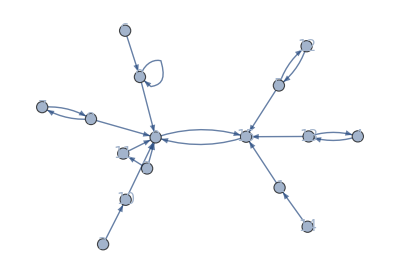

```mathematica
transitions = conditionTable[[1]][[All, 3]];
edges = Flatten[Table[Table[transitions[[i]][[j]][[1]],{j,1,Length[transitions[[i]]]}],{i,1,Length[transitions]}]];
GraphPlot[edges, VertexLabels->Placed[Automatic,Center],VertexSize->.4,  DirectedEdges->True, ImageSize->Full, VertexLabelStyle -> 15]
```

```mathematica
(*Here will will get all graphs and their regions*)
(*We will initialise with the transitions from 0 and their regions*)
transitions = conditionTable[[1]][[All, 3]];
possible = Table[{transitions[[1]][[j]][[1]],transitions[[1]][[j]][[2]]},{j,1,Length[transitions[[1]]]}];
graphAssumptions = {1 > r > s > 0};

Do[
(*Updated possible after adding the next round of transitions*)
next = {};
Do[
Do[
(*Print[i," ",j," ", k];*)
(*Add a new transition to possible[[k]]*)
function = Assuming[graphAssumptions,Simplify[And[possible[[k]][[2]],transitions[[i]][[j]][[2]]]]];
(*If the new region is non empty, add possible[[k]] with the new transition to next*)
If[(function===False)==False,
next = AppendTo[next,{Flatten[{possible[[k]][[1]],transitions[[i]][[j]][[1]]}],Assuming[graphAssumptions,Simplify[And[possible[[k]][[2]],function]]]}];
];
,{k,1,Length[possible]}];
,{j,1,Length[transitions[[i]]]}];
possible = next;
,{i,2,16}];        

(*Add the restrictions*)
Graphs = Table[{possible[[i]][[1]],Simplify[possible[[i]][[2]]&&( And @@ graphAssumptions)]},{i,1,Length[possible]}];

(*Delete regions which will now become empty*)
Graphs = DeleteCases[Graphs,{_,False}];
Print[Length[Graphs]];
Grid[Table[{i,Graphs[[i]][[1]],Graphs[[i]][[2]]},{i,1,Length[Graphs]}], Frame->All]

edgeslist = Graphs[[All,1]];
todraw = Graphs[[All,2]];
```

8

1 | {0→15,1→15,2→0,3→10,4→13,5→12,6→9,7→8,8→0,9→0,10→0,11→0,12→5,13→4,14→1,15→0} | 2 r<1+s&&3 s<1&&2 r≤1&&1>r>s>0
2 | {0→15,1→15,2→11,3→10,4→13,5→12,6→9,7→8,8→0,9→0,10→0,11→0,12→5,13→4,14→1,15→0} | 2 r<1+s&&1/3<s<1/2&&2 r≤1&&r>s
3 | {0→15,1→15,2→0,3→10,4→13,5→12,6→9,7→8,8→0,9→9,10→0,11→0,12→5,13→4,14→1,15→0} | 2 r<1+s&&3 s<1&&2 r>1&&1>r>s>0
4 | {0→15,1→15,2→11,3→10,4→13,5→12,6→9,7→8,8→0,9→9,10→0,11→0,12→5,13→4,14→1,15→0} | 2 r<1+s&&2 s<1&&2 r>1&&3 s>1&&1>r>s>0
5 | {0→15,1→15,2→11,3→10,4→13,5→12,6→9,7→8,8→7,9→9,10→0,11→0,12→5,13→4,14→1,15→0} | 2 r<1+s&&2 r>1&&2 s>1&&1>r>s>0
6 | {0→15,1→15,2→0,3→10,4→13,5→15,6→9,7→8,8→0,9→9,10→0,11→0,12→5,13→15,14→1,15→0} | 3 s<1&&2 r>1&&2 r>1+s&&1>r>s>0
7 | {0→15,1→15,2→11,3→10,4→13,5→15,6→9,7→8,8→0,9→9,10→0,11→0,12→5,13→15,14→1,15→0} | 2 s<1&&2 r>1&&2 r>1+s&&3 s>1&&1>r>s>0
8 | {0→15,1→15,2→11,3→10,4→13,5→15,6→9,7→8,8→7,9→9,10→0,11→0,12→5,13→15,14→1,15→0} | 2 r>1&&2 r>1+s&&2 s>1&&1>r>s>0

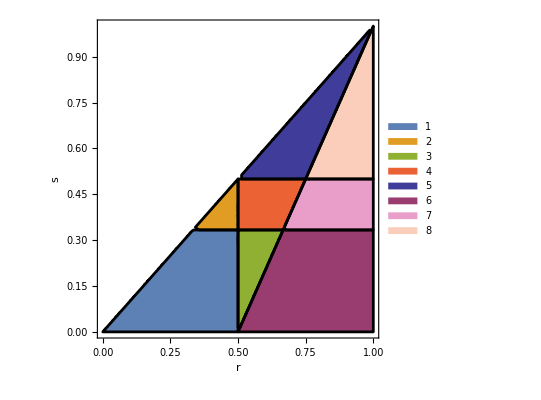

```mathematica
formulas = ReplaceAll[todraw, {r-> x,s->y}];
regionplotSHd75=RegionPlot[formulas,{x,0,1},{y,0,1},AxesLabel->Automatic,PlotStyle->{ColorData[97][1], ColorData[97][2], ColorData[97][3], ColorData[97][4], ColorData[1][1], ColorData[1][2], ColorData["MintColors"][2], ColorData[32][20]},BoundaryStyle->Black,PlotLegends->Placed[Automatic,{Left, Top}],PerformanceGoal->"Quality",FrameLabel->{"r","s"}, MaxRecursion->5]
```

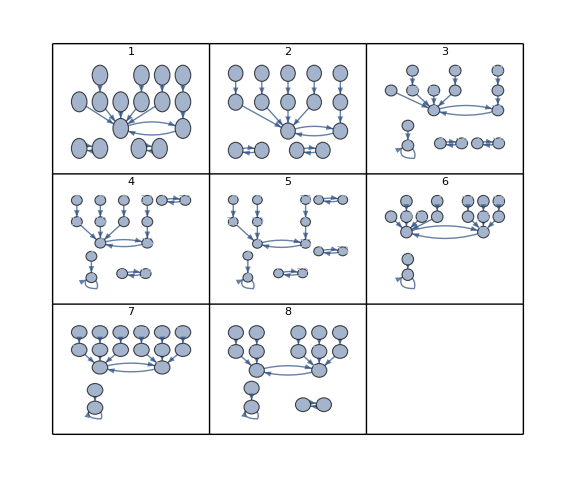

```mathematica
(*Make a grid with the different graphs (as square as possible)*)
grid = ArrayReshape[Table[Graphics[GraphPlot[edgeslist[[i]], VertexLabels->Placed[Automatic,Center],VertexSize->.75,  DirectedEdges->True,PlotLabel->i,PlotStyle->Thick, GraphLayout->"LayeredDigraphEmbedding"]],{i,1,Length[edgeslist]}],{Ceiling[Sqrt[Length[Graphs]]],Ceiling[Sqrt[Length[Graphs]]]}];

(*Convert the zeroes on the empty spaces in the grid to empty graphics*)
Do[Do[If[grid[[i]][[j]]==0, grid[[i]][[j]] = Graphics[{}]],{j,1,Length[grid[[i]]]}],{i,1,Length[grid]}]

(*Delete the empty rows*)
Do[If[grid[[i]] == ConstantArray[Graphics[{}],Length[grid[[i]]]],grid = grid[[1;;i-1]]; Break[]],{i,1,Length[grid]}]

(*Draw the grid*)
GraphicsGrid[grid,Frame->All,ImageSize->Large]

(*Function for drawing the regions of the graphs*)
drawregions[f_,n_]:=
Module[{new = n,formulas= f},
(*Replace the variables by the new values*)
formulas = ReplaceAll[formulas, {d->new,inside[[1]]->x,inside[[2]]->y}];
(*Make the region plot*)
 RegionPlot[formulas,{x,0,1},{y,0,1},AxesLabel->Automatic, PlotStyle->{Pink,Red,Orange,Yellow,Green,Cyan,Blue,Magenta,Purple,Brown,Gray,Black},BoundaryStyle->Black,PlotLegends->Automatic,PerformanceGoal->"Quality",FrameLabel->{inside[[1]],inside[[2]]}]
];

(*Draw the regions for various delta*)
Manipulate[drawregions[todraw,d],{d,0,1}]

(*Get the transition lines*)
test =possible[[All,2]];
test = test /. {And -> List, Or->List,Less -> Equal, LessEqual->Equal,Greater->Equal,GreaterEqual->Equal };
test = DeleteDuplicates[Flatten[test]];

(*Function for drawing the transition lines of the graphs*)
drawLines[f_,n_]:=
Module[{new = n,formulas= f},
formulas = ReplaceAll[formulas, {d->new,inside[[1]]->x,inside[[2]]->y}];
 ContourPlot[Evaluate @(formulas),{x,0,1},{y,0,1},FrameLabel->{inside[[1]],inside[[2]]},BoundaryStyle->{Pink,Red,Orange,Yellow,Green,Cyan,Blue,Magenta,Purple,Brown,Gray,Black},PlotLegends->test]
];

(*Draw the transition lines for various delta*)
Manipulate[drawLines[test,d],{d,0,1}]
```